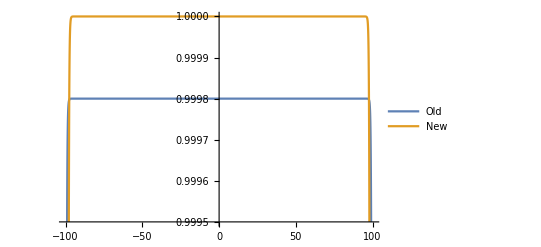

```mathematica
ϵ0 =5000; 
ϵ1=1;
ξ = 0.3;
h=100;
σ=1;
β = Sqrt[ϵ1/ϵ0];
P1[x_]=σ/ϵ0(ϵ0-1-1/β ⅇ^(-h/ξ)Cosh[x/ξ]);
P2[x_]=σ(1-ⅇ^(-h/ξ)Cosh[x/ξ]);
Show[Plot[{P1[x],P2[x]},{x,-100,100},{PlotLegends->Placed[{"Old", "New"},Below]}]]
```